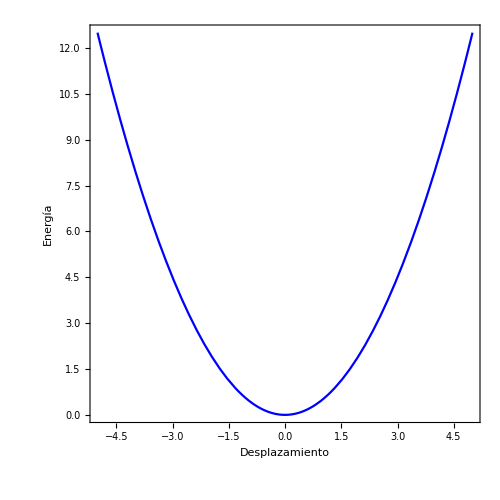

```mathematica
V[x_]= 1/2 Subscript[k, f] x^2;
condiciones={Subscript[k, f]->1,m->1,ℏ->1};
PlotEnergiaPotencial =
Plot[V[x] /. condiciones,{x,-5,5},Frame->True,PlotStyle->Blue, AspectRatio->1,FrameLabel->{"Desplazamiento","Energía"},LabelStyle->Directive[16,Black],Background->White,FrameStyle->Directive[Background->White],ImageSize->500]
```